```mathematica
SetDirectory[NotebookDirectory[]]
fontsize=12;
basestyle={FontFamily->"Latin Modern Roman",FontSize->fontsize};
label[s_]:=Style[s,Italic,fontsize+4]
texify[s_]:=StringReplace[ToString@TeXForm[s],{"\{"->"(","\}"->")"}]
Needs["MaTeX`"];
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"]
Needs["CustomTicks`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{orange}{rgb}{1,0.6,0}"}]
```

/Users/mkoster/Documents/QuatroFile/quarto_Reader_Week_1/figures

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color},\definecolor{orange}{rgb}{1,0.6,0}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

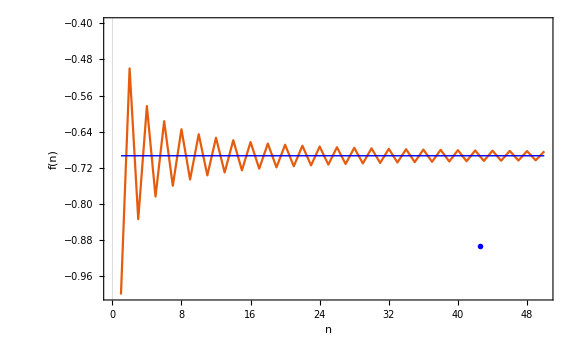

alternating_series.png

```mathematica
nmax=50;
vals=Transpose@{Range[nmax],Accumulate[(-1)^Range[nmax]/Range[nmax]]};

llp=ListLinePlot[vals,PlotRange->{-1,-0.4},Frame->True,FrameLabel->{"n","f(n)"},PlotTheme->"Scientific",ImageSize->Large,Epilog->{Blue,Thick,Line[{{1,-Log[2]},{nmax,-Log[2]}}],Inset[MaTeX["\color{blue} -\\ln(2)",Magnification->1.6],{0.85 nmax,-0.2-Log[2]}]}]
Export["alternating_series.png",%,ImageResolution->600]
```